```mathematica
Box2g[u_]:=Rectangle[{Min[First[u]],Min[Last[u]]},{Max[First[u]],Max[Last[u]]}];
Box2g[ix_,iy_,u_]:=Module[{value,min,max,mid},
value={u[[ix]],u[[iy]]};
min=Min/@value; max=Max/@value; mid=(Max[#]+Min[#])/2&/@value;
{Rectangle[min,max],PointSize[Large],Black,Point[mid]}
];

Pped2g[ix_,iy_, pped[x_,m_,u_]]:=Module[{x1,m1,u1},
x1={x[[ix]], x[[iy]]}; 
m1={{m[[ix,ix]], m[[ix,iy]]},{m[[iy,ix]], m[[iy,iy]]}};
u1={u[[ix]], u[[iy]]};
{GeometricTransformation[Rectangle[{Min[First[u1]],Min[Last[u1]]},{Max[First[u1]],Max[Last[u1]]}],AffineTransform[{m1,x1}]],
PointSize[Medium],Red,Point[x1]}
];

PpedD2g[ix_,iy_,pped2[x_,m_,u_, n_, v_]]:= Module[{x1,m1,u1,n1,v1},
x1={x[[ix]], x[[iy]]}; 
m1={{m[[ix,ix]], m[[ix,iy]]},{m[[iy,ix]], m[[iy,iy]]}};
u1={u[[ix]], u[[iy]]};
n1={{n[[ix,ix]], n[[ix,iy]]},{n[[iy,ix]], n[[iy,iy]]}};
v1={v[[ix]], v[[iy]]};
(*GeometricTransformation[Rectangle[{Min[First[u1]]+Min[First[v1]],Min[Last[u1]]+Min[Last[v1]]},{Max[First[u1]]+Max[First[v1]],Max[Last[u1]]+Max[Last[v1]]}],AffineTransform[{m1,x1}]]];*)
{GeometricTransformation[Rectangle[{Min[First[u1]],Min[Last[u1]]},{Max[First[u1]],Max[Last[u1]]}],AffineTransform[{m1,x1}]],
PointSize[Medium],Red,Point[x1]}];

(**)

pped2g[ix_,iy_,box[v_]]:=Module[{value,min,max,mid},
value={v[[ix]],v[[iy]]};
min=Min/@value; max=Max/@value; mid=(Max[#]+Min[#])/2&/@value;
{EdgeForm[{Thin,Black}],FaceForm[Opacity[0.1,LightGray]],Rectangle[min,max],PointSize[Small],Black,Point[mid]}
];
pped2g[ix_,iy_,pped[x_,m_,u_]]:=Module[{x1,m1,u1},
x1={x[[ix]], x[[iy]]}; 
m1={{m[[ix,ix]], m[[ix,iy]]},{m[[iy,ix]], m[[iy,iy]]}};
u1={u[[ix]], u[[iy]]};
{GeometricTransformation[Rectangle[{Min[First[u1]],Min[Last[u1]]},{Max[First[u1]],Max[Last[u1]]}],AffineTransform[{m1,x1}]],
PointSize[Medium],Red,Point[x1]}
];

pped2intv[iy_,box[v_]]:={Black,v[[iy]]};
pped2intv[iy_,pped[x_,m_,u_]]:=Module[{ix=1,x1,m1,u1},
x1={x[[ix]], x[[iy]]}; 
m1={{m[[ix,ix]], m[[ix,iy]]},{m[[iy,ix]], m[[iy,iy]]}};
u1={u[[ix]], u[[iy]]};
u1=m1.{Interval[{Min[First[u1]],Min[Last[u1]]}],Interval[{Max[First[u1]],Max[Last[u1]]}]}+x1;
{Red,u1[[2]][[1]]}
];

pipe2g[ix_,iy_,{t_,pped_}]:=Module[{res,value,min,max,mid},
If[ix>0,pped2g[ix,iy,pped],
res=pped2intv[iy,pped];
value={t,res[[2]]};
min=Min/@value; max=Max/@value; mid=(Max[#]+Min[#])/2&/@value;
{EdgeForm[{Thin,Black}],FaceForm[Opacity[0.1,LightGray]],Rectangle[min,max],PointSize[Large],res[[1]],Point[mid]}
]
];
```

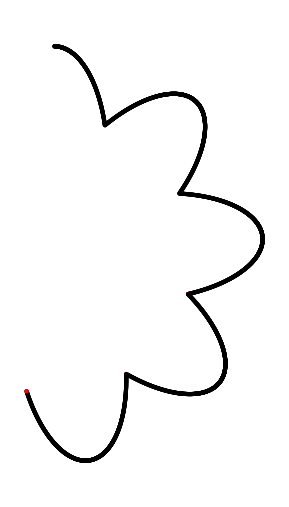

```mathematica
SetDirectory[NotebookDirectory[]];
list = <<../src_ocaml/pped.dat;
Graphics[pipe2g[1,2,#]& /@ list]
```

```mathematica
SetDirectory[NotebookDirectory[]];
list = <<../examples/pendulum.dat;
Graphics[pipe2g[0,1,#]& /@ list]
```